```mathematica
ToExpression["tr3={0,3,2,5};\ntr4={0,4,3,8,2,6,5,11};\ntr5={0,5,4,13,3,9,8,22,2,7,6,16,5,12,11,26};\ntr6={0,6,5,22,4,14,13,49,3,10,9,31,8,23,22,65,2,8,7,25,6,17,16,53,5,13,12,35,11,27,26,70};\ntr7={0,7,6,39,5,23,22,120,4,15,14,66,13,50,49,184,3,11,10,48,9,32,31,136,8,24,23,82,22,66,65,209,2,9,8,42,7,26,25,124,6,18,17,70,16,54,53,189,5,14,13,52,12,36,35,141,11,28,27,87,26,71,70,215};\ntr8={0,8,7,72,6,40,39,315,5,24,23,153,22,121,120,571,4,16,15,99,14,67,66,379,13,51,50,217,49,185,184,696,3,12,11,81,10,49,48,331,9,33,32,169,31,137,136,596,8,25,24,115,23,83,82,404,22,67,66,242,65,210,209,732,2,10,9,75,8,43,42,319,7,27,26,157,25,125,124,576,6,19,18,103,17,71,70,384,16,55,54,222,53,190,189,702,5,15,14,85,13,53,52,336,12,37,36,174,35,142,141,602,11,29,28,120,27,88,87,410,26,72,71,248,70,216,215,739};\ntr9={0,9,8,137,7,73,72,866,6,41,40,380,39,316,315,1890,5,25,24,218,23,154,153,1122,22,122,121,636,120,572,571,2515,4,17,16,164,15,100,99,930,14,68,67,444,66,380,379,2015,13,52,51,282,50,218,217,1247,49,186,185,761,184,697,696,2731,3,13,12,146,11,82,81,882,10,50,49,396,48,332,331,1915,9,34,33,234,32,170,169,1147,31,138,137,661,136,597,596,2551,8,26,25,180,24,116,115,955,23,84,83,469,82,405,404,2051,22,68,67,307,66,243,242,1283,65,211,210,797,209,733,732,2780,2,11,10,140,9,76,75,870,8,44,43,384,42,320,319,1895,7,28,27,222,26,158,157,1127,25,126,125,641,124,577,576,2521,6,20,19,168,18,104,103,935,17,72,71,449,70,385,384,2021,16,56,55,287,54,223,222,1253,53,191,190,767,189,703,702,2738,5,16,15,150,14,86,85,887,13,54,53,401,52,337,336,1921,12,38,37,239,36,175,174,1153,35,143,142,667,141,603,602,2558,11,30,29,185,28,121,120,961,27,89,88,475,87,411,410,2058,26,73,72,313,71,249,248,1290,70,217,216,804,215,740,739,2788};\ntr10={0,10,9,266,8,138,137,2453,7,74,73,995,72,867,866,6549,6,42,41,509,40,381,380,3477,39,317,316,2019,315,1891,1890,9674,5,26,25,347,24,219,218,2709,23,155,154,1251,153,1123,1122,7174,22,123,122,765,121,637,636,4102,120,573,572,2644,571,2516,2515,10970,4,18,17,293,16,165,164,2517,15,101,100,1059,99,931,930,6674,14,69,68,573,67,445,444,3602,66,381,380,2144,379,2016,2015,9890,13,53,52,411,51,283,282,2834,50,219,218,1376,217,1248,1247,7390,49,187,186,890,185,762,761,4318,184,698,697,2860,696,2732,2731,11313,3,14,13,275,12,147,146,2469,11,83,82,1011,81,883,882,6574,10,51,50,525,49,397,396,3502,48,333,332,2044,331,1916,1915,9710,9,35,34,363,33,235,234,2734,32,171,170,1276,169,1148,1147,7210,31,139,138,790,137,662,661,4138,136,598,597,2680,596,2552,2551,11019,8,27,26,309,25,181,180,2542,24,117,116,1084,115,956,955,6710,23,85,84,598,83,470,469,3638,82,406,405,2180,404,2052,2051,9939,22,69,68,436,67,308,307,2870,66,244,243,1412,242,1284,1283,7439,65,212,211,926,210,798,797,4367,209,734,733,2909,732,2781,2780,11377,2,12,11,269,10,141,140,2457,9,77,76,999,75,871,870,6554,8,45,44,513,43,385,384,3482,42,321,320,2024,319,1896,1895,9680,7,29,28,351,27,223,222,2714,26,159,158,1256,157,1128,1127,7180,25,127,126,770,125,642,641,4108,124,578,577,2650,576,2522,2521,10977,6,21,20,297,19,169,168,2522,18,105,104,1064,103,936,935,6680,17,73,72,578,71,450,449,3608,70,386,385,2150,384,2022,2021,9897,16,57,56,416,55,288,287,2840,54,224,223,1382,222,1254,1253,7397,53,192,191,896,190,768,767,4325,189,704,703,2867,702,2739,2738,11321,5,17,16,279,15,151,150,2474,14,87,86,1016,85,888,887,6580,13,55,54,530,53,402,401,3508,52,338,337,2050,336,1922,1921,9717,12,39,38,368,37,240,239,2740,36,176,175,1282,174,1154,1153,7217,35,144,143,796,142,668,667,4145,141,604,603,2687,602,2559,2558,11027,11,31,30,314,29,186,185,2548,28,122,121,1090,120,962,961,6717,27,90,89,604,88,476,475,3645,87,412,411,2187,410,2059,2058,9947,26,74,73,442,72,314,313,2877,71,250,249,1419,248,1291,1290,7447,70,218,217,933,216,805,804,4375,215,741,740,2917,739,2789,2788,11386};\ntr11={0,11,10,523,9,267,266,7084,8,139,138,2710,137,2454,2453,23468,7,75,74,1252,73,996,995,11180,72,868,867,6806,866,6550,6549,39093,6,43,42,766,41,510,509,8108,40,382,381,3734,380,3478,3477,26593,39,318,317,2276,316,2020,2019,14305,315,1892,1891,9931,1890,9675,9674,46869,5,27,26,604,25,348,347,7340,24,220,219,2966,218,2710,2709,24093,23,156,155,1508,154,1252,1251,11805,153,1124,1123,7431,1122,7175,7174,40389,22,124,123,1022,122,766,765,8733,121,638,637,4359,636,4103,4102,27889,120,574,573,2901,572,2645,2644,15601,571,2517,2516,11227,2515,10971,10970,49270,4,19,18,550,17,294,293,7148,16,166,165,2774,164,2518,2517,23593,15,102,101,1316,100,1060,1059,11305,99,932,931,6931,930,6675,6674,39309,14,70,69,830,68,574,573,8233,67,446,445,3859,444,3603,3602,26809,66,382,381,2401,380,2145,2144,14521,379,2017,2016,10147,2015,9891,9890,47212,13,54,53,668,52,412,411,7465,51,284,283,3091,282,2835,2834,24309,50,220,219,1633,218,1377,1376,12021,217,1249,1248,7647,1247,7391,7390,40732,49,188,187,1147,186,891,890,8949,185,763,762,4575,761,4319,4318,28232,184,699,698,3117,697,2861,2860,15944,696,2733,2732,11570,2731,11314,11313,49782,3,15,14,532,13,276,275,7100,12,148,147,2726,146,2470,2469,23493,11,84,83,1268,82,1012,1011,11205,81,884,883,6831,882,6575,6574,39129,10,52,51,782,50,526,525,8133,49,398,397,3759,396,3503,3502,26629,48,334,333,2301,332,2045,2044,14341,331,1917,1916,9967,1915,9711,9710,46918,9,36,35,620,34,364,363,7365,33,236,235,2991,234,2735,2734,24129,32,172,171,1533,170,1277,1276,11841,169,1149,1148,7467,1147,7211,7210,40438,31,140,139,1047,138,791,790,8769,137,663,662,4395,661,4139,4138,27938,136,599,598,2937,597,2681,2680,15650,596,2553,2552,11276,2551,11020,11019,49334,8,28,27,566,26,310,309,7173,25,182,181,2799,180,2543,2542,23629,24,118,117,1341,116,1085,1084,11341,115,957,956,6967,955,6711,6710,39358,23,86,85,855,84,599,598,8269,83,471,470,3895,469,3639,3638,26858,82,407,406,2437,405,2181,2180,14570,404,2053,2052,10196,2051,9940,9939,47276,22,70,69,693,68,437,436,7501,67,309,308,3127,307,2871,2870,24358,66,245,244,1669,243,1413,1412,12070,242,1285,1284,7696,1283,7440,7439,40796,65,213,212,1183,211,927,926,8998,210,799,798,4624,797,4368,4367,28296,209,735,734,3166,733,2910,2909,16008,732,2782,2781,11634,2780,11378,11377,49863,2,13,12,526,11,270,269,7088,10,142,141,2714,140,2458,2457,23473,9,78,77,1256,76,1000,999,11185,75,872,871,6811,870,6555,6554,39099,8,46,45,770,44,514,513,8113,43,386,385,3739,384,3483,3482,26599,42,322,321,2281,320,2025,2024,14311,319,1897,1896,9937,1895,9681,9680,46876,7,30,29,608,28,352,351,7345,27,224,223,2971,222,2715,2714,24099,26,160,159,1513,158,1257,1256,11811,157,1129,1128,7437,1127,7181,7180,40396,25,128,127,1027,126,771,770,8739,125,643,642,4365,641,4109,4108,27896,124,579,578,2907,577,2651,2650,15608,576,2523,2522,11234,2521,10978,10977,49278,6,22,21,554,20,298,297,7153,19,170,169,2779,168,2523,2522,23599,18,106,105,1321,104,1065,1064,11311,103,937,936,6937,935,6681,6680,39316,17,74,73,835,72,579,578,8239,71,451,450,3865,449,3609,3608,26816,70,387,386,2407,385,2151,2150,14528,384,2023,2022,10154,2021,9898,9897,47220,16,58,57,673,56,417,416,7471,55,289,288,3097,287,2841,2840,24316,54,225,224,1639,223,1383,1382,12028,222,1255,1254,7654,1253,7398,7397,40740,53,193,192,1153,191,897,896,8956,190,769,768,4582,767,4326,4325,28240,189,705,704,3124,703,2868,2867,15952,702,2740,2739,11578,2738,11322,11321,49791,5,18,17,536,16,280,279,7105,15,152,151,2731,150,2475,2474,23499,14,88,87,1273,86,1017,1016,11211,85,889,888,6837,887,6581,6580,39136,13,56,55,787,54,531,530,8139,53,403,402,3765,401,3509,3508,26636,52,339,338,2307,337,2051,2050,14348,336,1923,1922,9974,1921,9718,9717,46926,12,40,39,625,38,369,368,7371,37,241,240,2997,239,2741,2740,24136,36,177,176,1539,175,1283,1282,11848,174,1155,1154,7474,1153,7218,7217,40446,35,145,144,1053,143,797,796,8776,142,669,668,4402,667,4146,4145,27946,141,605,604,2944,603,2688,2687,15658,602,2560,2559,11284,2558,11028,11027,49343,11,32,31,571,30,315,314,7179,29,187,186,2805,185,2549,2548,23636,28,123,122,1347,121,1091,1090,11348,120,963,962,6974,961,6718,6717,39366,27,91,90,861,89,605,604,8276,88,477,476,3902,475,3646,3645,26866,87,413,412,2444,411,2188,2187,14578,410,2060,2059,10204,2058,9948,9947,47285,26,75,74,699,73,443,442,7508,72,315,314,3134,313,2878,2877,24366,71,251,250,1676,249,1420,1419,12078,248,1292,1291,7704,1290,7448,7447,40805,70,219,218,1190,217,934,933,9006,216,806,805,4632,804,4376,4375,28305,215,742,741,3174,740,2918,2917,16017,739,2790,2789,11643,2788,11387,11386,49873};\ntr12={0,12,11,1036,10,524,523,20719,9,268,267,7597,266,7085,7084,86255,8,140,139,3223,138,2711,2710,37103,137,2455,2454,23981,2453,23469,23468,164380,7,76,75,1765,74,1253,1252,24815,73,997,996,11693,995,11181,11180,101880,72,869,868,7319,867,6807,6806,52728,866,6551,6550,39606,6549,39094,39093,211036,6,44,43,1279,42,767,766,21743,41,511,510,8621,509,8109,8108,89380,40,383,382,4247,381,3735,3734,40228,380,3479,3478,27106,3477,26594,26593,172156,39,319,318,2789,317,2277,2276,27940,316,2021,2020,14818,2019,14306,14305,109656,315,1893,1892,10444,1891,9932,9931,60504,1890,9676,9675,47382,9674,46870,46869,227843,5,28,27,1117,26,605,604,20975,25,349,348,7853,347,7341,7340,86880,24,221,220,3479,219,2967,2966,37728,218,2711,2710,24606,2709,24094,24093,165676,23,157,156,2021,155,1509,1508,25440,154,1253,1252,12318,1251,11806,11805,103176,153,1125,1124,7944,1123,7432,7431,54024,1122,7176,7175,40902,7174,40390,40389,213437,22,125,124,1535,123,1023,1022,22368,122,767,766,9246,765,8734,8733,90676,121,639,638,4872,637,4360,4359,41524,636,4104,4103,28402,4102,27890,27889,174557,120,575,574,3414,573,2902,2901,29236,572,2646,2645,16114,2644,15602,15601,112057,571,2518,2517,11740,2516,11228,11227,62905,2515,10972,10971,49783,10970,49271,49270,231939,4,20,19,1063,18,551,550,20783,17,295,294,7661,293,7149,7148,86380,16,167,166,3287,165,2775,2774,37228,164,2519,2518,24106,2517,23594,23593,164596,15,103,102,1829,101,1317,1316,24940,100,1061,1060,11818,1059,11306,11305,102096,99,933,932,7444,931,6932,6931,52944,930,6676,6675,39822,6674,39310,39309,211379,14,71,70,1343,69,831,830,21868,68,575,574,8746,573,8234,8233,89596,67,447,446,4372,445,3860,3859,40444,444,3604,3603,27322,3602,26810,26809,172499,66,383,382,2914,381,2402,2401,28156,380,2146,2145,15034,2144,14522,14521,109999,379,2018,2017,10660,2016,10148,10147,60847,2015,9892,9891,47725,9890,47213,47212,228355,13,55,54,1181,53,669,668,21100,52,413,412,7978,411,7466,7465,87096,51,285,284,3604,283,3092,3091,37944,282,2836,2835,24822,2834,24310,24309,166019,50,221,220,2146,219,1634,1633,25656,218,1378,1377,12534,1376,12022,12021,103519,217,1250,1249,8160,1248,7648,7647,54367,1247,7392,7391,41245,7390,40733,40732,213949,49,189,188,1660,187,1148,1147,22584,186,892,891,9462,890,8950,8949,91019,185,764,763,5088,762,4576,4575,41867,761,4320,4319,28745,4318,28233,28232,175069,184,700,699,3630,698,3118,3117,29579,697,2862,2861,16457,2860,15945,15944,112569,696,2734,2733,12083,2732,11571,11570,63417,2731,11315,11314,50295,11313,49783,49782,232668,3,16,15,1045,14,533,532,20735,13,277,276,7613,275,7101,7100,86280,12,149,148,3239,147,2727,2726,37128,146,2471,2470,24006,2469,23494,23493,164416,11,85,84,1781,83,1269,1268,24840,82,1013,1012,11718,1011,11206,11205,101916,81,885,884,7344,883,6832,6831,52764,882,6576,6575,39642,6574,39130,39129,211085,10,53,52,1295,51,783,782,21768,50,527,526,8646,525,8134,8133,89416,49,399,398,4272,397,3760,3759,40264,396,3504,3503,27142,3502,26630,26629,172205,48,335,334,2814,333,2302,2301,27976,332,2046,2045,14854,2044,14342,14341,109705,331,1918,1917,10480,1916,9968,9967,60553,1915,9712,9711,47431,9710,46919,46918,227907,9,37,36,1133,35,621,620,21000,34,365,364,7878,363,7366,7365,86916,33,237,236,3504,235,2992,2991,37764,234,2736,2735,24642,2734,24130,24129,165725,32,173,172,2046,171,1534,1533,25476,170,1278,1277,12354,1276,11842,11841,103225,169,1150,1149,7980,1148,7468,7467,54073,1147,7212,7211,40951,7210,40439,40438,213501,31,141,140,1560,139,1048,1047,22404,138,792,791,9282,790,8770,8769,90725,137,664,663,4908,662,4396,4395,41573,661,4140,4139,28451,4138,27939,27938,174621,136,600,599,3450,598,2938,2937,29285,597,2682,2681,16163,2680,15651,15650,112121,596,2554,2553,11789,2552,11277,11276,62969,2551,11021,11020,49847,11019,49335,49334,232020,8,29,28,1079,27,567,566,20808,26,311,310,7686,309,7174,7173,86416,25,183,182,3312,181,2800,2799,37264,180,2544,2543,24142,2542,23630,23629,164645,24,119,118,1854,117,1342,1341,24976,116,1086,1085,11854,1084,11342,11341,102145,115,958,957,7480,956,6968,6967,52993,955,6712,6711,39871,6710,39359,39358,211443,23,87,86,1368,85,856,855,21904,84,600,599,8782,598,8270,8269,89645,83,472,471,4408,470,3896,3895,40493,469,3640,3639,27371,3638,26859,26858,172563,82,408,407,2950,406,2438,2437,28205,405,2182,2181,15083,2180,14571,14570,110063,404,2054,2053,10709,2052,10197,10196,60911,2051,9941,9940,47789,9939,47277,47276,228436,22,71,70,1206,69,694,693,21136,68,438,437,8014,436,7502,7501,87145,67,310,309,3640,308,3128,3127,37993,307,2872,2871,24871,2870,24359,24358,166083,66,246,245,2182,244,1670,1669,25705,243,1414,1413,12583,1412,12071,12070,103583,242,1286,1285,8209,1284,7697,7696,54431,1283,7441,7440,41309,7439,40797,40796,214030,65,214,213,1696,212,1184,1183,22633,211,928,927,9511,926,8999,8998,91083,210,800,799,5137,798,4625,4624,41931,797,4369,4368,28809,4367,28297,28296,175150,209,736,735,3679,734,3167,3166,29643,733,2911,2910,16521,2909,16009,16008,112650,732,2783,2782,12147,2781,11635,11634,63498,2780,11379,11378,50376,11377,49864,49863,232768,2,14,13,1039,12,527,526,20723,11,271,270,7601,269,7089,7088,86260,10,143,142,3227,141,2715,2714,37108,140,2459,2458,23986,2457,23474,23473,164386,9,79,78,1769,77,1257,1256,24820,76,1001,1000,11698,999,11186,11185,101886,75,873,872,7324,871,6812,6811,52734,870,6556,6555,39612,6554,39100,39099,211043,8,47,46,1283,45,771,770,21748,44,515,514,8626,513,8114,8113,89386,43,387,386,4252,385,3740,3739,40234,384,3484,3483,27112,3482,26600,26599,172163,42,323,322,2794,321,2282,2281,27946,320,2026,2025,14824,2024,14312,14311,109663,319,1898,1897,10450,1896,9938,9937,60511,1895,9682,9681,47389,9680,46877,46876,227851,7,31,30,1121,29,609,608,20980,28,353,352,7858,351,7346,7345,86886,27,225,224,3484,223,2972,2971,37734,222,2716,2715,24612,2714,24100,24099,165683,26,161,160,2026,159,1514,1513,25446,158,1258,1257,12324,1256,11812,11811,103183,157,1130,1129,7950,1128,7438,7437,54031,1127,7182,7181,40909,7180,40397,40396,213445,25,129,128,1540,127,1028,1027,22374,126,772,771,9252,770,8740,8739,90683,125,644,643,4878,642,4366,4365,41531,641,4110,4109,28409,4108,27897,27896,174565,124,580,579,3420,578,2908,2907,29243,577,2652,2651,16121,2650,15609,15608,112065,576,2524,2523,11747,2522,11235,11234,62913,2521,10979,10978,49791,10977,49279,49278,231948,6,23,22,1067,21,555,554,20788,20,299,298,7666,297,7154,7153,86386,19,171,170,3292,169,2780,2779,37234,168,2524,2523,24112,2522,23600,23599,164603,18,107,106,1834,105,1322,1321,24946,104,1066,1065,11824,1064,11312,11311,102103,103,938,937,7450,936,6938,6937,52951,935,6682,6681,39829,6680,39317,39316,211387,17,75,74,1348,73,836,835,21874,72,580,579,8752,578,8240,8239,89603,71,452,451,4378,450,3866,3865,40451,449,3610,3609,27329,3608,26817,26816,172507,70,388,387,2920,386,2408,2407,28163,385,2152,2151,15041,2150,14529,14528,110007,384,2024,2023,10667,2022,10155,10154,60855,2021,9899,9898,47733,9897,47221,47220,228364,16,59,58,1186,57,674,673,21106,56,418,417,7984,416,7472,7471,87103,55,290,289,3610,288,3098,3097,37951,287,2842,2841,24829,2840,24317,24316,166027,54,226,225,2152,224,1640,1639,25663,223,1384,1383,12541,1382,12029,12028,103527,222,1256,1255,8167,1254,7655,7654,54375,1253,7399,7398,41253,7397,40741,40740,213958,53,194,193,1666,192,1154,1153,22591,191,898,897,9469,896,8957,8956,91027,190,770,769,5095,768,4583,4582,41875,767,4327,4326,28753,4325,28241,28240,175078,189,706,705,3637,704,3125,3124,29587,703,2869,2868,16465,2867,15953,15952,112578,702,2741,2740,12091,2739,11579,11578,63426,2738,11323,11322,50304,11321,49792,49791,232678,5,19,18,1049,17,537,536,20740,16,281,280,7618,279,7106,7105,86286,15,153,152,3244,151,2732,2731,37134,150,2476,2475,24012,2474,23500,23499,164423,14,89,88,1786,87,1274,1273,24846,86,1018,1017,11724,1016,11212,11211,101923,85,890,889,7350,888,6838,6837,52771,887,6582,6581,39649,6580,39137,39136,211093,13,57,56,1300,55,788,787,21774,54,532,531,8652,530,8140,8139,89423,53,404,403,4278,402,3766,3765,40271,401,3510,3509,27149,3508,26637,26636,172213,52,340,339,2820,338,2308,2307,27983,337,2052,2051,14861,2050,14349,14348,109713,336,1924,1923,10487,1922,9975,9974,60561,1921,9719,9718,47439,9717,46927,46926,227916,12,41,40,1138,39,626,625,21006,38,370,369,7884,368,7372,7371,86923,37,242,241,3510,240,2998,2997,37771,239,2742,2741,24649,2740,24137,24136,165733,36,178,177,2052,176,1540,1539,25483,175,1284,1283,12361,1282,11849,11848,103233,174,1156,1155,7987,1154,7475,7474,54081,1153,7219,7218,40959,7217,40447,40446,213510,35,146,145,1566,144,1054,1053,22411,143,798,797,9289,796,8777,8776,90733,142,670,669,4915,668,4403,4402,41581,667,4147,4146,28459,4145,27947,27946,174630,141,606,605,3457,604,2945,2944,29293,603,2689,2688,16171,2687,15659,15658,112130,602,2561,2560,11797,2559,11285,11284,62978,2558,11029,11028,49856,11027,49344,49343,232030,11,33,32,1084,31,572,571,20814,30,316,315,7692,314,7180,7179,86423,29,188,187,3318,186,2806,2805,37271,185,2550,2549,24149,2548,23637,23636,164653,28,124,123,1860,122,1348,1347,24983,121,1092,1091,11861,1090,11349,11348,102153,120,964,963,7487,962,6975,6974,53001,961,6719,6718,39879,6717,39367,39366,211452,27,92,91,1374,90,862,861,21911,89,606,605,8789,604,8277,8276,89653,88,478,477,4415,476,3903,3902,40501,475,3647,3646,27379,3645,26867,26866,172572,87,414,413,2957,412,2445,2444,28213,411,2189,2188,15091,2187,14579,14578,110072,410,2061,2060,10717,2059,10205,10204,60920,2058,9949,9948,47798,9947,47286,47285,228446,26,76,75,1212,74,700,699,21143,73,444,443,8021,442,7509,7508,87153,72,316,315,3647,314,3135,3134,38001,313,2879,2878,24879,2877,24367,24366,166092,71,252,251,2189,250,1677,1676,25713,249,1421,1420,12591,1419,12079,12078,103592,248,1293,1292,8217,1291,7705,7704,54440,1290,7449,7448,41318,7447,40806,40805,214040,70,220,219,1703,218,1191,1190,22641,217,935,934,9519,933,9007,9006,91092,216,807,806,5145,805,4633,4632,41940,804,4377,4376,28818,4375,28306,28305,175160,215,743,742,3687,741,3175,3174,29652,740,2919,2918,16530,2917,16018,16017,112660,739,2791,2790,12156,2789,11644,11643,63508,2788,11388,11387,50386,11386,49874,49873,232779};\n"]
```

```mathematica
tr3
```

{0,3,2,5}

```mathematica
trs={tr3,tr4,tr5,tr6,tr7,tr8,tr9,tr10,tr11,tr12};
```

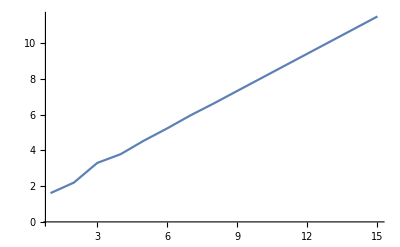

```mathematica
ListPlot[Map[Log,Drop[Psums[tr5],1]],Joined->True,PlotRange->All]
```

```mathematica
Map[First,trs]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
Map[#[[2]]&,trs]
```

{3,4,5,6,7,8,9,10,11,12}

```mathematica
Map[#[[3]]&,trs]
```

{2,3,4,5,6,7,8,9,10,11}

```mathematica
Map[#[[4]]&,trs]
```

{5,8,13,22,39,72,137,266,523,1036}

```mathematica
Map[#[[5]]&,Drop[trs,1]]
```

{2,3,4,5,6,7,8,9,10}

```mathematica
Map[#[[6]]&,Drop[trs,1]]
```

{6,9,14,23,40,73,138,267,524}

```mathematica
Map[#[[7]]&,Drop[trs,1]]
```

{5,8,13,22,39,72,137,266,523}

```mathematica
Map[#[[8]]&,Drop[trs,1]]
```

{11,22,49,120,315,866,2453,7084,20719}

```mathematica
Map[#[[9]]&,Drop[trs,2]]
```

{2,3,4,5,6,7,8,9}

```mathematica
Map[#[[10]]&,Drop[trs,2]]
```

{7,10,15,24,41,74,139,268}

```mathematica
Map[#[[11]]&,Drop[trs,2]]
```

{6,9,14,23,40,73,138,267}

```mathematica
Map[#[[16]]&,Drop[trs,2]]
```

{26,65,184,571,1890,6549,23468,86255}

```mathematica
trs[[2]]
Differences[%]
```

{0,4,3,8,2,6,5,11}

{4,-1,5,-6,4,-1,6}

```mathematica
Quotient[3,2]
```

1

```mathematica
trs[[4]]
First[Differences[{First[#],Reverse[Last[#]]}&[halfs[%]]]]
First[Differences[{First[#],Reverse[Last[#]]}&[halfs[%]]]]
First[Differences[{First[#],Reverse[Last[#]]}&[halfs[%]]]]
```

{0,6,5,22,4,14,13,49,3,10,9,31,8,23,22,65,2,8,7,25,6,17,16,53,5,13,12,35,11,27,26,70}

{70,20,22,-11,31,-2,0,-44,50,6,8,-25,17,-16,-14,-63}

{-133,-34,-38,28,-56,10,6,94}

{227,40,48,-84}

```mathematica
Total[{First[#],Reverse[Last[#]]}&[halfs[trs[[4]]]]]
Total[{First[#],Reverse[Last[#]]}&[halfs[%]]]
Total[{First[#],Reverse[Last[#]]}&[halfs[%]]]
Total[{First[#],Reverse[Last[#]]}&[halfs[%]]]
```

{70,32,32,33,39,26,26,54,56,26,26,37,33,30,30,67}

{137,62,62,66,76,52,52,110}

{247,114,114,142}

{389,228}

```mathematica
halfs[l_]:=Partition[l,Quotient[Length[l],2]]
```

```mathematica
halfs[{1,2,3,4}]
```

{{1,2},{3,4}}

```mathematica
Table[Map[#[[i]]&,Drop[trs,2]],{i,1,16}]//TableForm
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
13 | 22 | 39 | 72 | 137 | 266 | 523 | 1036
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
9 | 14 | 23 | 40 | 73 | 138 | 267 | 524
8 | 13 | 22 | 39 | 72 | 137 | 266 | 523
22 | 49 | 120 | 315 | 866 | 2453 | 7084 | 20719
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
7 | 10 | 15 | 24 | 41 | 74 | 139 | 268
6 | 9 | 14 | 23 | 40 | 73 | 138 | 267
16 | 31 | 66 | 153 | 380 | 995 | 2710 | 7597
5 | 8 | 13 | 22 | 39 | 72 | 137 | 266
12 | 23 | 50 | 121 | 316 | 867 | 2454 | 7085
11 | 22 | 49 | 120 | 315 | 866 | 2453 | 7084
26 | 65 | 184 | 571 | 1890 | 6549 | 23468 | 86255

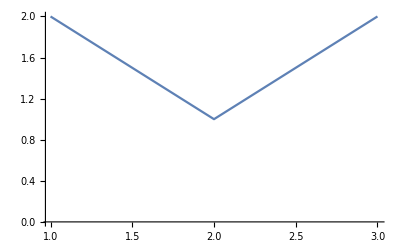
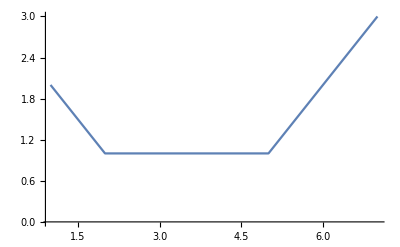
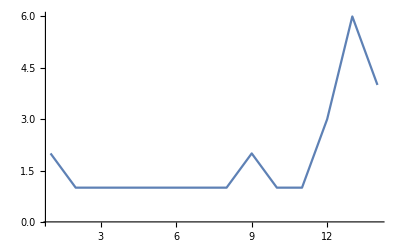
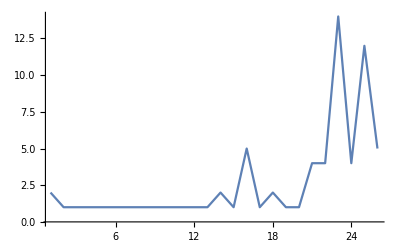
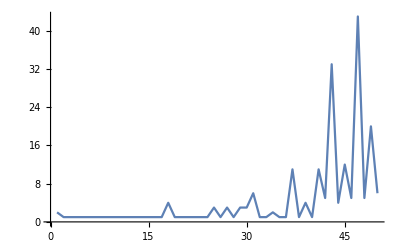
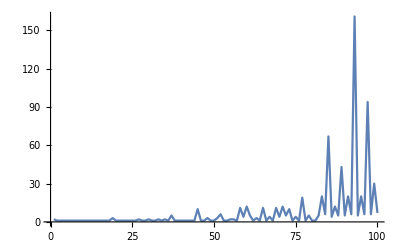
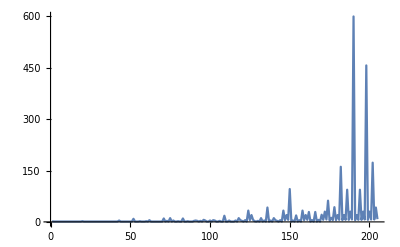
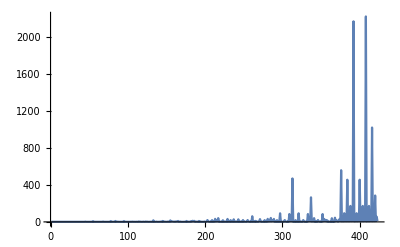

```mathematica
Map[ListPlot[Differences[Sort[DeleteDuplicates[#]]],Joined->True,PlotRange->All]&,trs]
```

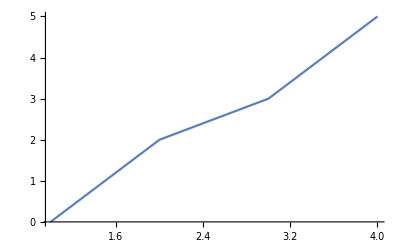
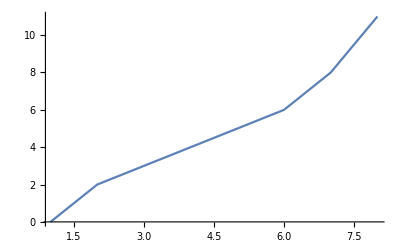
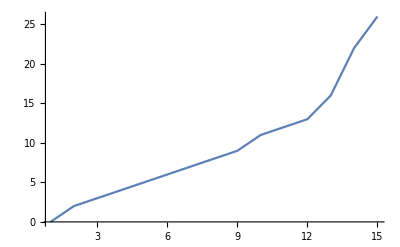
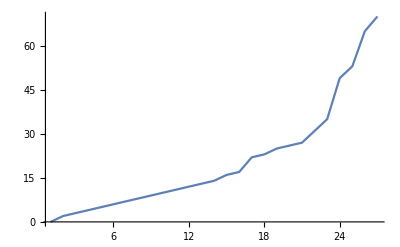
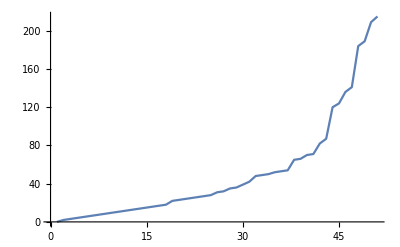
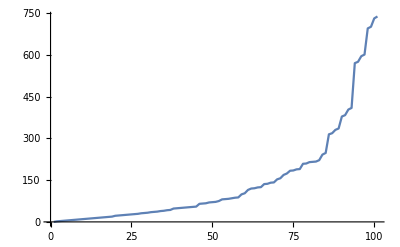
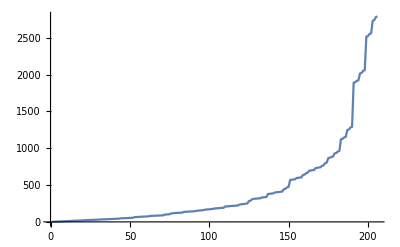
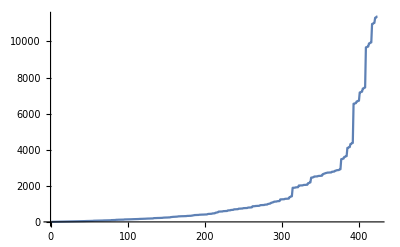

```mathematica
Map[ListPlot[Sort[DeleteDuplicates[#]],Joined->True,PlotRange->All]&,trs]
```

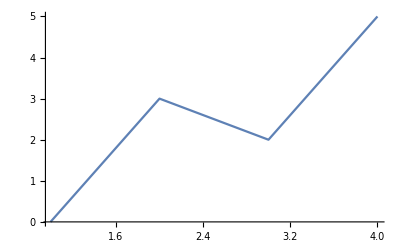
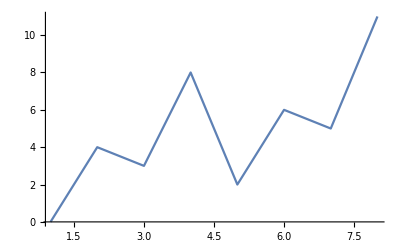
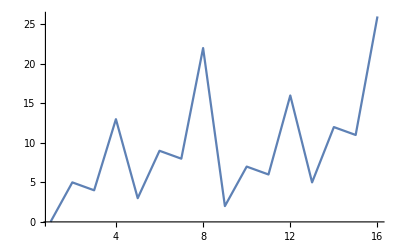
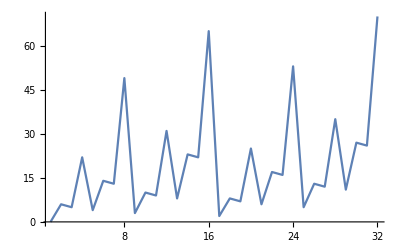
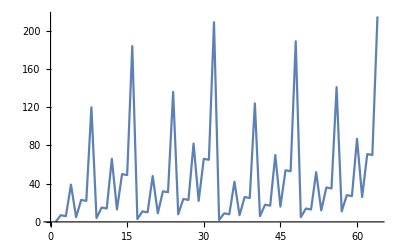
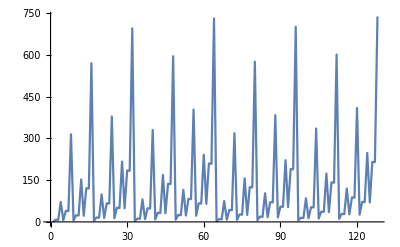
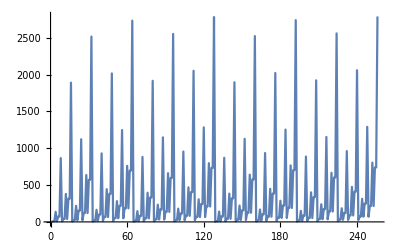
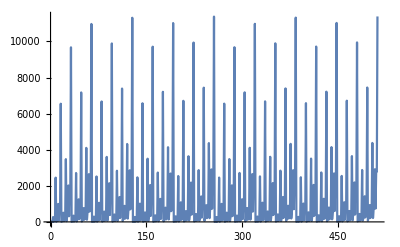

```mathematica
Map[ListPlot[#,Joined->True,PlotRange->All]&,trs]
```

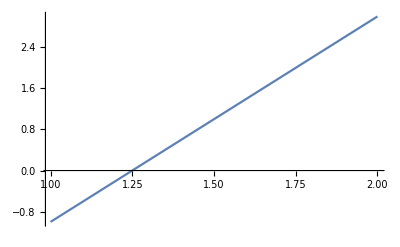
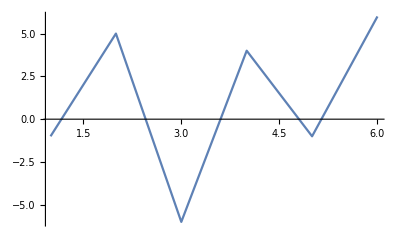
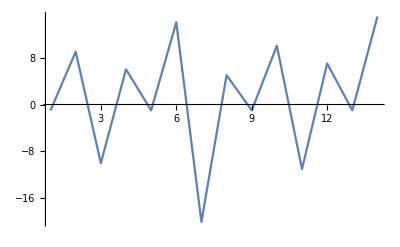
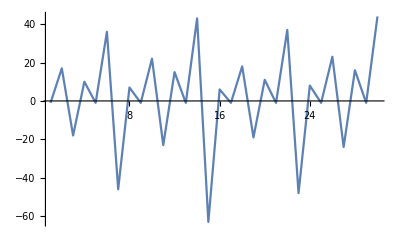
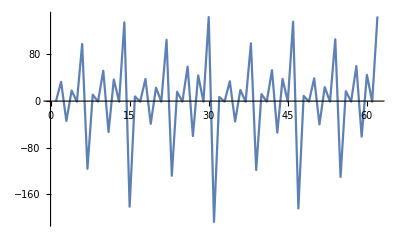
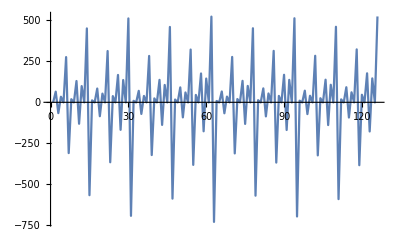
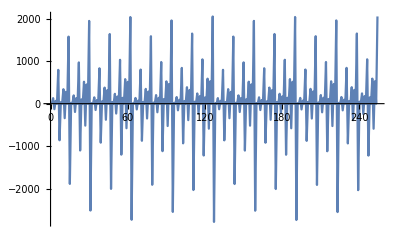
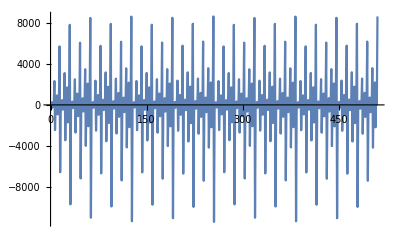

```mathematica
Map[ListPlot[Differences[Drop[#,1]],Joined->True,PlotRange->All]&,trs]
```

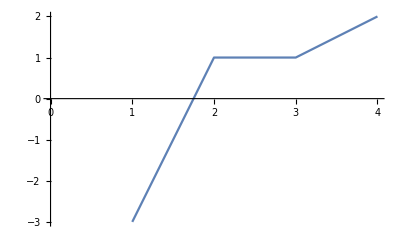
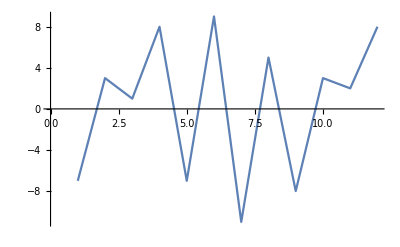
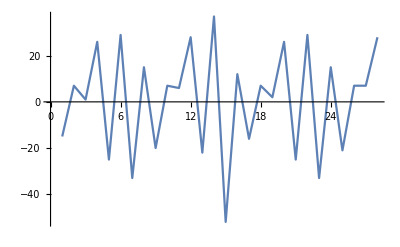
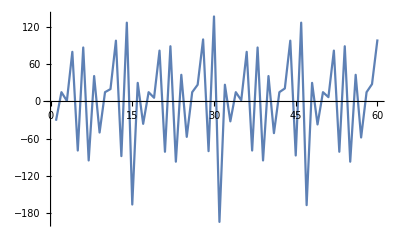
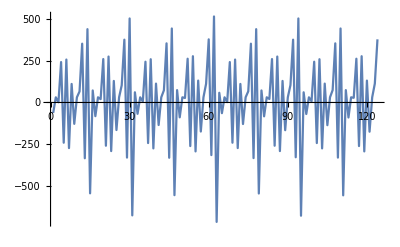
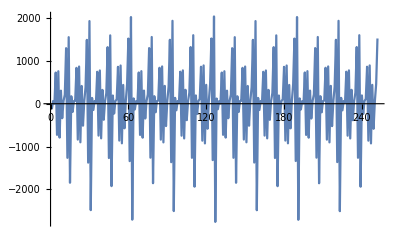
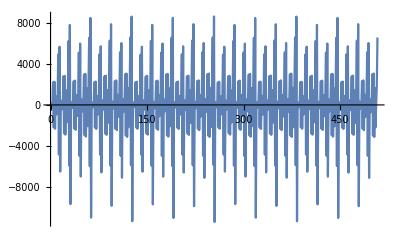
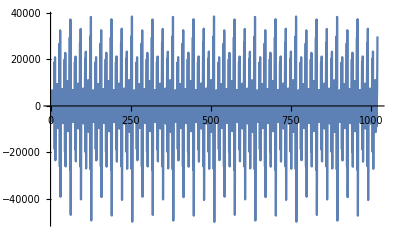
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[ListPlot[Differences[Map[Abs,Differences[Map[Abs,Differences[Drop[#,1]]]]]],Joined->True]&,trs]
```

```mathematica
Map[Differences,{tr3,tr4,tr5,tr6,tr7,tr8,tr9,tr10,tr11,tr12}]//Column
```

```mathematica
Psums[l_]:=Piecewise[{{{}, Length[l]==0}, {Prepend[Psums[l[[1]]+Drop[l,1]],l[[1]]], True}}]
```

```mathematica
Psums[{1,2,3,4,5}]
```

{1,3,7,15,31}

```mathematica
Prepend[{1,2,3},1]
```

{1,1,2,3}

```mathematica
{0}
{1}
{2}
{2,1}
{3}
{3,1}
{3,2}
{3,2,1}
{4}
{4,1}
{4,2}
{4,2,1}
{4,3}
{4,3,1}
{4,3,2}
{4,3,2,1}
{5}
{5,1}
{5,2}
{5,2,1}
{5,3}
{5,3,1}
{5,3,2}
{5,3,2,1}
{5,4}
{5,4,1}
{5,4,2}
{5,4,2,1}
{5,4,3}
{5,4,3,1}
{5,4,3,2}
{5,4,3,2,1}
```

```mathematica
00{0}
01{1}
02{2}
03{2,1}
04{3}
05{3,1}
06{3,2}
07{3,2,1}
08{4}
09{4,1}
10{4,2}
11{4,2,1}
12{4,3}
13{4,3,1}
14{4,3,2}
15{4,3,2,1}
16{5}
17{5,1}
18{5,2}
19{5,2,1}
20{5,3}
21{5,3,1}
22{5,3,2}
23{5,3,2,1}
24{5,4}
25{5,4,1}
26{5,4,2}
27{5,4,2,1}
28{5,4,3}
29{5,4,3,1}
30{5,4,3,2}
31{5,4,3,2,1}
32{6}
```

```mathematica
f[2^n≤x≤2^(n+1)-1,1]==n+1
f[
```

```mathematica
f[2^n]=={n+1}
f[2^n≤x≤2^(n+1)-1,1]==n+1
Mod[x,2]==Mod[f[x,-1],2]
f[2^n+(1≤m≤2^n-1)]==(n+1):f[m]
f[2^n+(1≤m≤2^n-1),1]==(n+1)
f[2^n+2^(n-1)+(0≤m≤2^(n-1)),2]==n

g[2^n]==n+1
g[2^n+1]==n+3
```

```mathematica
{Subscript[a, i]|1≤i≤n}->Subscript[a, 1]+∑_(i=2)^n i^Subscript[a, i]
```

```mathematica
"sequence _[]=[0]
sequence st (b:bs) |b==0=sequence (st-1) bs
			       |b==1=(st-1):sequence (st-1) bs";
g[x_,n_]:=Piecewise[{{□, EvenQ[x]}, {□, OddQ[x]}}]
```

```mathematica
s[st_,bs_]:=Piecewise[{{{}, bs=={}}, {s[st-1,Drop[bs,1]], bs[[1]]==0}, {Prepend[s[st-1,Drop[bs,1]],st-1], bs[[1]]==1}}]
s[5,{1,0,1,1}]
```

{4,2,1}

```mathematica
allone[n_]:=Table[Prepend[s[n,PadLeft[IntegerDigits[i,2],n-1]],n],{i,0,2^(n-1)-1}]
allone[5]
all[n_]:=Flatten[Table[allone[m],{m,0,n}],1]
all[5]
```

{{5},{5,1},{5,2},{5,2,1},{5,3},{5,3,1},{5,3,2},{5,3,2,1},{5,4},{5,4,1},{5,4,2},{5,4,2,1},{5,4,3},{5,4,3,1},{5,4,3,2},{5,4,3,2,1}}

{{1},{2},{2,1},{3},{3,1},{3,2},{3,2,1},{4},{4,1},{4,2},{4,2,1},{4,3},{4,3,1},{4,3,2},{4,3,2,1},{5},{5,1},{5,2},{5,2,1},{5,3},{5,3,1},{5,3,2},{5,3,2,1},{5,4},{5,4,1},{5,4,2},{5,4,2,1},{5,4,3},{5,4,3,1},{5,4,3,2},{5,4,3,2,1}}

```mathematica
Flatten[Position[Map[Drop[#,1]&,all[6]],{}]]
Position[Map[Drop[#,1]&,all[6]],{1}]
Position[Map[Drop[#,1]&,all[6]],{2}]
Position[Map[Drop[#,1]&,all[6]],{2,1}]
```

{1,2,4,8,16,32}

{{3},{5},{9},{17},{33}}

{{6},{10},{18},{34}}

{{7},{11},{19},{35}}

```mathematica
bitsenum[all[6]]//Column
```

{1,{0,0,0,0,0,1},{1}}
{2,{0,0,0,0,1,0},{2}}
{1,{0,0,0,0,1,1},{2,1}}
{3,{0,0,0,1,0,0},{3}}
{1,{0,0,0,1,0,1},{3,1}}
{2,{0,0,0,1,1,0},{3,2}}
{1,{0,0,0,1,1,1},{3,2,1}}
{4,{0,0,1,0,0,0},{4}}
{1,{0,0,1,0,0,1},{4,1}}
{2,{0,0,1,0,1,0},{4,2}}
{1,{0,0,1,0,1,1},{4,2,1}}
{3,{0,0,1,1,0,0},{4,3}}
{1,{0,0,1,1,0,1},{4,3,1}}
{2,{0,0,1,1,1,0},{4,3,2}}
{1,{0,0,1,1,1,1},{4,3,2,1}}
{5,{0,1,0,0,0,0},{5}}
{1,{0,1,0,0,0,1},{5,1}}
{2,{0,1,0,0,1,0},{5,2}}
{1,{0,1,0,0,1,1},{5,2,1}}
{3,{0,1,0,1,0,0},{5,3}}
{1,{0,1,0,1,0,1},{5,3,1}}
{2,{0,1,0,1,1,0},{5,3,2}}
{1,{0,1,0,1,1,1},{5,3,2,1}}
{4,{0,1,1,0,0,0},{5,4}}
{1,{0,1,1,0,0,1},{5,4,1}}
{2,{0,1,1,0,1,0},{5,4,2}}
{1,{0,1,1,0,1,1},{5,4,2,1}}
{3,{0,1,1,1,0,0},{5,4,3}}
{1,{0,1,1,1,0,1},{5,4,3,1}}
{2,{0,1,1,1,1,0},{5,4,3,2}}
{1,{0,1,1,1,1,1},{5,4,3,2,1}}
{6,{1,0,0,0,0,0},{6}}
{1,{1,0,0,0,0,1},{6,1}}
{2,{1,0,0,0,1,0},{6,2}}
{1,{1,0,0,0,1,1},{6,2,1}}
{3,{1,0,0,1,0,0},{6,3}}
{1,{1,0,0,1,0,1},{6,3,1}}
{2,{1,0,0,1,1,0},{6,3,2}}
{1,{1,0,0,1,1,1},{6,3,2,1}}
{4,{1,0,1,0,0,0},{6,4}}
{1,{1,0,1,0,0,1},{6,4,1}}
{2,{1,0,1,0,1,0},{6,4,2}}
{1,{1,0,1,0,1,1},{6,4,2,1}}
{3,{1,0,1,1,0,0},{6,4,3}}
{1,{1,0,1,1,0,1},{6,4,3,1}}
{2,{1,0,1,1,1,0},{6,4,3,2}}
{1,{1,0,1,1,1,1},{6,4,3,2,1}}
{5,{1,1,0,0,0,0},{6,5}}
{1,{1,1,0,0,0,1},{6,5,1}}
{2,{1,1,0,0,1,0},{6,5,2}}
{1,{1,1,0,0,1,1},{6,5,2,1}}
{3,{1,1,0,1,0,0},{6,5,3}}
{1,{1,1,0,1,0,1},{6,5,3,1}}
{2,{1,1,0,1,1,0},{6,5,3,2}}
{1,{1,1,0,1,1,1},{6,5,3,2,1}}
{4,{1,1,1,0,0,0},{6,5,4}}
{1,{1,1,1,0,0,1},{6,5,4,1}}
{2,{1,1,1,0,1,0},{6,5,4,2}}
{1,{1,1,1,0,1,1},{6,5,4,2,1}}
{3,{1,1,1,1,0,0},{6,5,4,3}}
{1,{1,1,1,1,0,1},{6,5,4,3,1}}
{2,{1,1,1,1,1,0},{6,5,4,3,2}}
{1,{1,1,1,1,1,1},{6,5,4,3,2,1}}

```mathematica
bg[n_]:=n+∑_(i=2)^n i^(n+1-i)
6+2^5+3^4+4^3+5^2+6^1
bg[6]
```

214

214

```mathematica
bitdistfromR[x_]:=Max[Flatten[Position[IntegerDigits[x,2],1]]]
```

```mathematica
bitsenum[l_]:=Block[{len=Length[l]},
Block[{pad=Ceiling[Log2[len]]},
Table[{1+pad-Max[Position[PadLeft[IntegerDigits[i,2],pad],1]],PadLeft[IntegerDigits[i,2],pad],l[[i]]},{i,1,len}]]]
```

```mathematica
bitsenum[Map[If[Length[#]>0,#[[-1]],0]&,all[5]]]//Column
```

{1,{0,0,0,0,1},1}
{2,{0,0,0,1,0},2}
{1,{0,0,0,1,1},1}
{3,{0,0,1,0,0},3}
{1,{0,0,1,0,1},1}
{2,{0,0,1,1,0},2}
{1,{0,0,1,1,1},1}
{4,{0,1,0,0,0},4}
{1,{0,1,0,0,1},1}
{2,{0,1,0,1,0},2}
{1,{0,1,0,1,1},1}
{3,{0,1,1,0,0},3}
{1,{0,1,1,0,1},1}
{2,{0,1,1,1,0},2}
{1,{0,1,1,1,1},1}
{5,{1,0,0,0,0},5}
{1,{1,0,0,0,1},1}
{2,{1,0,0,1,0},2}
{1,{1,0,0,1,1},1}
{3,{1,0,1,0,0},3}
{1,{1,0,1,0,1},1}
{2,{1,0,1,1,0},2}
{1,{1,0,1,1,1},1}
{4,{1,1,0,0,0},4}
{1,{1,1,0,0,1},1}
{2,{1,1,0,1,0},2}
{1,{1,1,0,1,1},1}
{3,{1,1,1,0,0},3}
{1,{1,1,1,0,1},1}
{2,{1,1,1,1,0},2}
{1,{1,1,1,1,1},1}

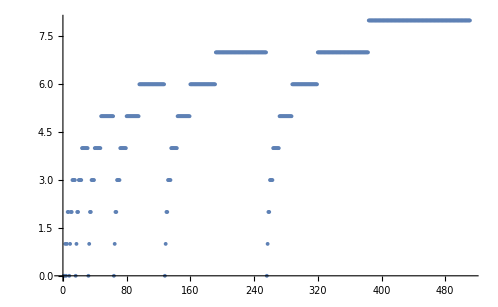

```mathematica
ListPlot[Map[If[Length[#]>1,#[[2]],0]&,all[9]],Joined->False]
```

```mathematica
bitsenum[Map[If[Length[#]>1,#[[2]],0]&,all[6]]]//Column
```

{1,{0,0,0,0,0,1},0}
{2,{0,0,0,0,1,0},0}
{1,{0,0,0,0,1,1},1}
{3,{0,0,0,1,0,0},0}
{1,{0,0,0,1,0,1},1}
{2,{0,0,0,1,1,0},2}
{1,{0,0,0,1,1,1},2}
{4,{0,0,1,0,0,0},0}
{1,{0,0,1,0,0,1},1}
{2,{0,0,1,0,1,0},2}
{1,{0,0,1,0,1,1},2}
{3,{0,0,1,1,0,0},3}
{1,{0,0,1,1,0,1},3}
{2,{0,0,1,1,1,0},3}
{1,{0,0,1,1,1,1},3}
{5,{0,1,0,0,0,0},0}
{1,{0,1,0,0,0,1},1}
{2,{0,1,0,0,1,0},2}
{1,{0,1,0,0,1,1},2}
{3,{0,1,0,1,0,0},3}
{1,{0,1,0,1,0,1},3}
{2,{0,1,0,1,1,0},3}
{1,{0,1,0,1,1,1},3}
{4,{0,1,1,0,0,0},4}
{1,{0,1,1,0,0,1},4}
{2,{0,1,1,0,1,0},4}
{1,{0,1,1,0,1,1},4}
{3,{0,1,1,1,0,0},4}
{1,{0,1,1,1,0,1},4}
{2,{0,1,1,1,1,0},4}
{1,{0,1,1,1,1,1},4}
{6,{1,0,0,0,0,0},0}
{1,{1,0,0,0,0,1},1}
{2,{1,0,0,0,1,0},2}
{1,{1,0,0,0,1,1},2}
{3,{1,0,0,1,0,0},3}
{1,{1,0,0,1,0,1},3}
{2,{1,0,0,1,1,0},3}
{1,{1,0,0,1,1,1},3}
{4,{1,0,1,0,0,0},4}
{1,{1,0,1,0,0,1},4}
{2,{1,0,1,0,1,0},4}
{1,{1,0,1,0,1,1},4}
{3,{1,0,1,1,0,0},4}
{1,{1,0,1,1,0,1},4}
{2,{1,0,1,1,1,0},4}
{1,{1,0,1,1,1,1},4}
{5,{1,1,0,0,0,0},5}
{1,{1,1,0,0,0,1},5}
{2,{1,1,0,0,1,0},5}
{1,{1,1,0,0,1,1},5}
{3,{1,1,0,1,0,0},5}
{1,{1,1,0,1,0,1},5}
{2,{1,1,0,1,1,0},5}
{1,{1,1,0,1,1,1},5}
{4,{1,1,1,0,0,0},5}
{1,{1,1,1,0,0,1},5}
{2,{1,1,1,0,1,0},5}
{1,{1,1,1,0,1,1},5}
{3,{1,1,1,1,0,0},5}
{1,{1,1,1,1,0,1},5}
{2,{1,1,1,1,1,0},5}
{1,{1,1,1,1,1,1},5}

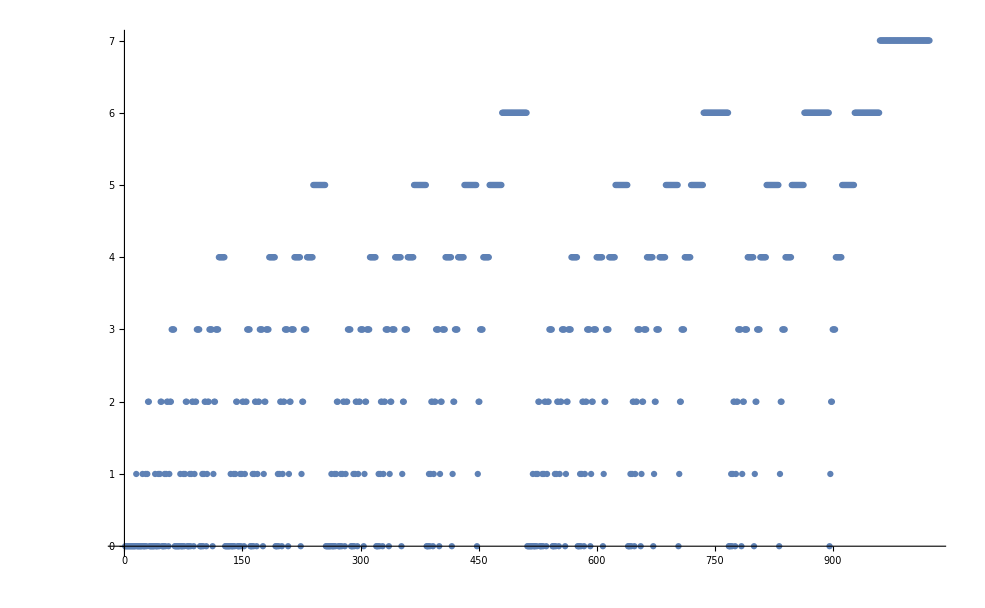

```mathematica
Map[If[Length[#]>3,#[[4]],0]&,all[10]]//ListPlot
```

```mathematica
IntegerDigits[31,2]
```

{1,1,1,1,1}

This is key: All the H(x)=2’s end at 2^i, all the H(x)=3’s end at 3^i, etc. This fact, once noticed, is easily provable.

```mathematica
0;0;00000{0+0}
1;1;00001{1+0}
2;1;00010{2+0}
2;2;00011{2+2^1}
3;1;00100{3+0}
3;2;00101{3+2^1}
3;2;00110{3+2^2}
3;3;00111{3+2^2+3^1}
4;1;01000{4+0}
4;2;01001{4+2^1}
4;2;01010{4+2^2}
4;3;01011{4+2^2+3^1}
4;2;01100{4+2^3}
4;3;01101{4+2^3+3^1}
4;3;01110{4+2^3+3^2}
4;4;01111{4+2^3+3^2+4^1}
5;1;10000{5+0}
5;2;10001{5+2^1}
5;2;10010{5+2^2}
5;3;10011{5+2^2+3^1}
5;2;10100{5+2^3}
5;3;10101{5+2^3+3^1}
5;3;10110{5+2^3+3^2}
5;4;10111{5+2^3+3^2+4^1}
5;2;11000{5+2^4}
5;3;11001{5+2^4+3^1}
5;3;11010{5+2^4+3^2}
5;4;11011{5+2^4+3^2+4^1}
5;3;11100{5+2^4+3^3}
5;4;11101{5+2^4+3^3+4^1}
5;4;11110{5+2^4+3^3+4^2}
5;5;11111{5+2^4+3^3+4^2+5^1}
```

```mathematica
Table[BellB[i]+1,{i,0,5}]
```

{2,2,3,6,16,53}

```mathematica
g[2^n-1]==∑_(i=1)^(n-2) (BellB[i]+1)
```

```mathematica
03{1}
05{1}
06{2}
07{2}
09{1}
10{2}
11{2}
12{3}
13{3}
14{3}
15{3}
17{1}
18{2}
19{2}
20{3}
21{3}
22{3}
23{3}
24{4}
25{4}
26{4}
27{4}
28{4}
29{4}
30{4}
31{4}
```

{{{0,0,1,1,1},1},{{0,1,0,1,1},1},{{0,1,1,0,1},1},{{0,1,1,1,0},2},{{0,1,1,1,1},2},{{1,0,0,1,1},1},{{1,0,1,0,1},1},{{1,0,1,1,0},2},{{1,0,1,1,1},2},{{1,1,0,0,1},1},{{1,1,0,1,0},2},{{1,1,0,1,1},2},{{1,1,1,0,0},3},{{1,1,1,0,1},3},{{1,1,1,1,0},3},{{1,1,1,1,1},3}}

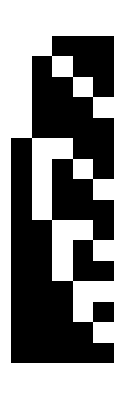

```mathematica
Map[{PadLeft[IntegerDigits[#[[1]],2],5],#[[2]][[1]]}&,{{07,{1}},
{11,{1}},
{13,{1}},
{14,{2}},
{15,{2}},
{19,{1}},
{21,{1}},
{22,{2}},
{23,{2}},
{25,{1}},
{26,{2}},
{27,{2}},
{28,{3}},
{29,{3}},
{30,{3}},
{31,{3}}}]
Map[First,%]//ArrayPlot
```